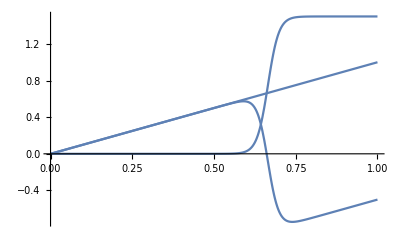

```mathematica
(* Figure out the acceleration profile of a space elevator that goes at ag m/s^2 until turn around point, then goes at 0 m/s^2 to the interior person, within the spinning environment.*)
(*In units where r=1=1 km and g=1=10 m/s^2, 1 time unit is 10 s*)
r=1;
g=1;
a=1.5;
s=30;
ac[x_]:=g(x/r)+(a g)/2(Tanh[s(r0-x)]-1);
Plot[({-(a g)/2(Tanh[s(r0-x)]-1),g(x/r),ac[x]})/.r0->0.6,{x,0,r}]
```

{5.02038}

{-7.08837}

{5.0041}

{1.41651}

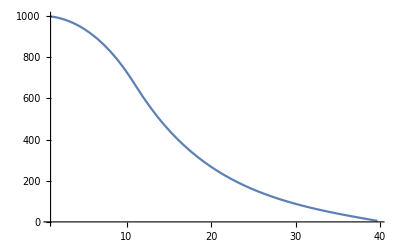

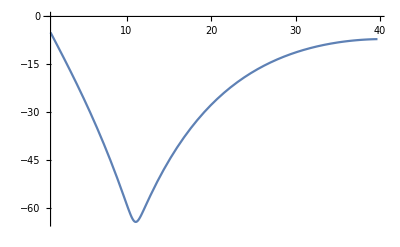

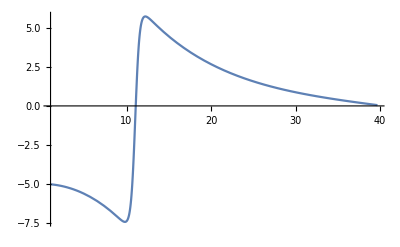

```mathematica
r0=0.665;
t0=3.97;
res=NDSolve[{x''[t]==(ac[x[t]]),x[0]==r, x'[0]==0},x,{t,0,t0}];
x[t0]*1000/.res
x'[t0]*100/.res
accel=1/2(x'[t0]*100/.res)^2/(x[t0]*1000/.res)
time=(x'[t0]*100/.res)/-accel
Plot[Evaluate[{x[t/10]*1000}/. res],{t,1,10t0},PlotStyle->Automatic]
Plot[Evaluate[{x'[t/10]*1000/10}/. res],{t,1,10t0},PlotStyle->Automatic]
Plot[Evaluate[{x''[t/10]*1000/100}/. res],{t,1,10t0},PlotStyle->Automatic]
```